Alexandria Taylor, 4/15/2020

## Assignment : Modify the Mathematica solution to hydrogen atoms such that it will give the results in SI units instead of atomic units.

A) Use this program to calculate three lowest energy levels (1 s, 2 s, and 3 s) of hydrogen atom, express the result in eV units. (0.25 pts)

```mathematica
E0 = En /.  {Z -> 1, n -> 1}
```

{Energy→-1/2}

```mathematica
Quantity[-1/2,"HartreeEnergy"]
```

-1/2 E_h

```mathematica
Print["E_(1  S)=",UnitConvert[Quantity[-1/2,"HartreeEnergy"],"Electronvolts"]]
```

E_(1  S)=-13.605693123 eV

```mathematica
E0 = En /.  {Z -> 1, n -> 2}
```

{Energy→-1/8}

```mathematica
Quantity[-1/8,"HartreeEnergy"]
```

-1/8 E_h

```mathematica
Print["E_(2  S)=",UnitConvert[Quantity[-1/8,"HartreeEnergy"],"Electronvolts"]]
```

E_(2  S)=-3.4014232807 eV

```mathematica
E0 = En /.  {Z -> 1, n -> 3}
```

{Energy→-1/18}

```mathematica
Quantity[-1/18,"HartreeEnergy"]
```

-1/18 E_h

```mathematica
Print["E_(3  S)=",UnitConvert[Quantity[-1/18,"HartreeEnergy"],"Electronvolts"]]
```

E_(3  S)=-1.5117436803 eV

B) Plot the corresponding wave functions and radial probability densities. (0.25 pts)

```mathematica
Ψ0 = Simplify[Ψ[r] /. sol2 /. {Z -> 1, n -> 1}] /. (C[1]+C[2]) -> C0
```

C0 ⅇ^-r

```mathematica
Ψ1 = Simplify[Ψ[r] /. sol2 /. {Z -> 1, n -> 2}] /. (2C[1]-C[2]) -> C1
```

1/2 C1 ⅇ^(-r/2) (-2+r)

```mathematica
Ψ2 = Simplify[Ψ[r] /. sol2 /. {Z -> 1, n -> 3}]/.(6C[1]+C[2])->C2
```

1/27 C2 ⅇ^(-r/3) (27-18 r+2 r^2)

```mathematica
constant0 = Solve[∫_0^∞ r^2 Ψ0^2 ⅆr== 1,C0]
```

{{C0→-2},{C0→2}}

```mathematica
constant1 = Solve[∫_0^∞ r^2 Ψ1^2 ⅆr== 1,C1]
```

{{C1→-1/(√2)},{C1→1/(√2)}}

```mathematica
constant2= Solve[∫_0^∞ r^2 Ψ2^2 ⅆr== 1,C2]
```

{{C2→-2/(3 √3)},{C2→2/(3 √3)}}

```mathematica
Subscript[ΨH, 0][r_] = Ψ0 /. Last[constant0]
```

2 ⅇ^-r

```mathematica
Subscript[ΨH, 1][r_] = Ψ1 /. Last[constant1]
```

(ⅇ^(-r/2) (-2+r))/(2 √2)

```mathematica
Subscript[ΨH, 2][r_] = Ψ2 /. Last[constant2]
```

(2 ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √3)

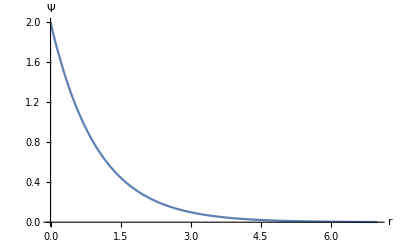

```mathematica
Plot[Subscript[ΨH, 0][r],{r, 0, 7}, PlotRange -> All, AxesLabel -> {r, Ψ}]
```

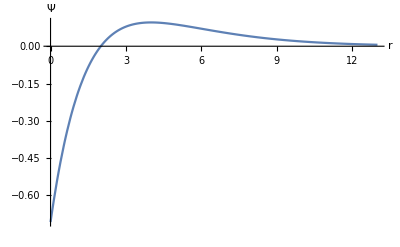

```mathematica
Plot[Subscript[ΨH, 1][r], {r, 0, 13}, PlotRange -> All, AxesLabel -> {r, Ψ}]
```

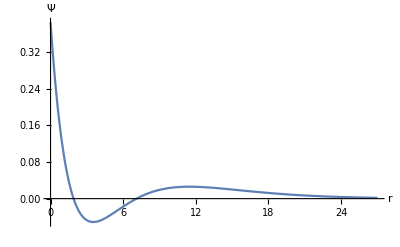

```mathematica
Plot[Subscript[ΨH, 2][r], {r, 0, 27}, PlotRange -> All, AxesLabel -> {r, Ψ}]
```

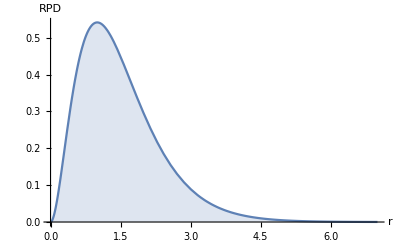

```mathematica
Plot[r^2 (Subscript[ΨH, 0][r])^2, {r, 0, 7}, PlotRange -> All, Filling->Axis, AxesLabel -> {r,RPD}]
```

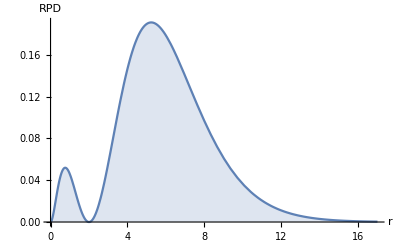

```mathematica
Plot[r^2 (Subscript[ΨH, 1][r])^2, {r, 0, 17}, PlotRange -> All, Filling->Axis, AxesLabel -> {r,RPD}]
```

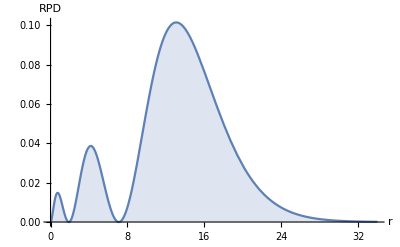

```mathematica
Plot[r^2 (Subscript[ΨH, 2][r])^2, {r, 0, 34}, PlotRange -> All, Filling->Axis, AxesLabel -> {r,RPD}]
```

C) Calculate the wavelength associated with transition of hydrogen atom from its ground state to the first excited state. (0.25 pts)

```mathematica
1/Subscript[λ, hydrogencalc]=R(1/Subscript[n, f]^2-1/Subscript[n, i]^2);   R= Quantity[1.0974 10^7,1/("Meters")];
```

```mathematica
1/Subscript[λ, hydrogencalc]=(1.0974 10^7)(1/2^2-1/1^2)
```

```mathematica
Quantity[-8.2305*^6, 1/("Meters")]
```

```mathematica
Subscript[λ, hydrogencalc]=1/(8.2305*^6)
```

```mathematica
Print ["λ_hydrogencalc=",1.2149930137901707*^-7(10^9 nm)]
```

λ_hydrogencalc=121.499 nm

D) Compare the results with experimental data and discuss the accuracy of the analytical solution provided by Mathematica. (0.25 pts)

```mathematica
ΔE=Subscript[E, 2S]-Subscript[E, 1S]
```

10.204269842 eV

```mathematica
UnitConvert[ΔE,"Joules"]
```

1.6349042708×10^-18 J

```mathematica
Subscript[λ, hydrogenexp]= hc/ΔE;
h=Quantity[6.626 10^-34,"Joules""Seconds"];c=Quantity[3 10^8,("Meters")/("Seconds")]
```

1.21585×10^-7 m

```mathematica
Print["λ_hydrogenexp=", UnitConvert[Quantity[1.2158510045323047*^-7,"Meters"],"nanometers"]]
```

λ_hydrogenexp=121.585 nm

```mathematica
AbsError = [Subscript[λ, hydrogencalc]-Subscript[λ, hydrogenexp]];
```

```mathematica
Print["AbsError=",121.499nm-121.585nm]
```

AbsError=-0.086 nm

The absolute error of 0.086 nm between the calculated and experimental wavelengths for hydrogen shows that the computational method chosen is a suitable application for accurate measurements of classical mechanics.